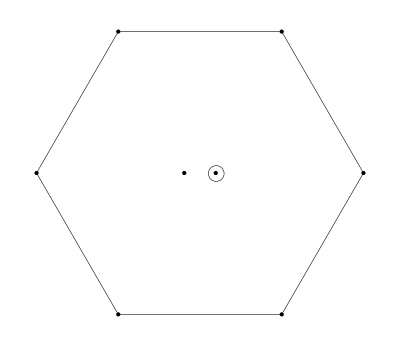

Y=0,  I_3=0

-4uuūū+8ddd̄d̄-4sss̄s̄-2(us+su)(ūs̄+s̄ū)+(sd+ds)(s̄d̄+d̄s̄)+(ud+du)(ūd̄+d̄ū)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C γ^μ s_b) ((d̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((d̄)_b)^T)+(s_a^T C γ^μ d_b) ((d̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((d̄)_b)^T)+(d_a^T C γ^μ s_b) ((s̄)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((s̄)_b)^T)+(s_a^T C γ^μ d_b) ((s̄)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((s̄)_b)^T)+8 (d_a^T C γ^μ d_b) ((d̄)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((d̄)_b)^T)+(d_a^T C γ^μ u_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+(u_a^T C γ^μ d_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+4 (s_a^T C γ^μ s_b) ((s̄)_a γ^μ C((s̄)_b)^T-(s̄)_b γ^μ C((s̄)_a)^T)+2 (s_a^T C γ^μ u_b) ((s̄)_a γ^μ C((ū)_b)^T-(s̄)_b γ^μ C((ū)_a)^T)+2 (u_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T-(s̄)_b γ^μ C((ū)_a)^T)+2 (s_a^T C γ^μ u_b) ((ū)_a γ^μ C((s̄)_b)^T-(ū)_b γ^μ C((s̄)_a)^T)+2 (u_a^T C γ^μ s_b) ((ū)_a γ^μ C((s̄)_b)^T-(ū)_b γ^μ C((s̄)_a)^T)+4 (u_a^T C γ^μ u_b) ((ū)_a γ^μ C((ū)_b)^T-(ū)_b γ^μ C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
8 (d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 d)-8 (d̄ γ^μ d d̄ γ^μ d)+16 (d̄(γ̄)^5 d d̄(γ̄)^5 d)+2 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s)+2 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d s̄ γ^μ s)-2 (d̄ γ^μ s s̄ γ^μ d)+4 (d̄(γ̄)^5 s s̄(γ̄)^5 d)+4 (s̄(γ̄)^5 s) (d̄(γ̄)^5 d-2 (ū(γ̄)^5 u))+4 (s̄ 1s) (2 (ū 1u)-d̄ 1d)-4 (d̄ 1s s̄ 1d)+2 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+2 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d ū γ^μ u)-2 (d̄ γ^μ u ū γ^μ d)+4 (d̄(γ̄)^5 d ū(γ̄)^5 u)+4 (d̄(γ̄)^5 u ū(γ̄)^5 d)-4 (d̄ 1d ū 1u)-4 (d̄ 1u ū 1d)-16 (d̄ 1d d̄ 1d)-4 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)+4 (s̄ γ^μ s s̄ γ^μ s)-8 (s̄(γ̄)^5 s s̄(γ̄)^5 s)-4 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)-4 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)+4 (s̄ γ^μ s ū γ^μ u)+4 (s̄ γ^μ u ū γ^μ s)-8 (s̄(γ̄)^5 u ū(γ̄)^5 s)+8 (s̄ 1u ū 1s)+8 (s̄ 1s s̄ 1s)-4 (ū(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)+4 (ū γ^μ u ū γ^μ u)-8 (ū(γ̄)^5 u ū(γ̄)^5 u)+8 (ū 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(32 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(8 π^5)+(⟨ ū u⟩ log(-q^2/μ^2) (m_d+4 m_s-5 m_u) q^4)/(3 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (2 m_d-m_s-m_u) q^4)/(3 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (m_d-5 m_s+4 m_u) q^4)/(3 π^4)-(656 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(200 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(200 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(125 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(144 π^6)-(40 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(40 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(304 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(256 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)+(8 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)+(8 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)+(8 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(64 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(32 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(8 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)+(32 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)+(64 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(464 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(152 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(152 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(11 ⟨ d̄ Gd⟩^2)/(3 π^2 q^2)-(11 ⟨ s̄ Gs⟩^2)/(12 π^2 q^2)-(11 ⟨ ū Gu⟩^2)/(12 π^2 q^2)-(28 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)-(28 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(256 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)-(11 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(48 π^2 q^2)-(11 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)-(11 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(12 π^2 q^2)-(1024 ⟨ d̄ d⟩^3 m_d)/q^2-(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (2 m_d-47 m_s))/(9 q^2)-(256 ⟨ s̄ s⟩^3 m_s)/q^2-(32 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (97 m_d+2 m_s))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_d-47 m_u))/(9 q^2)-(256 ⟨ ū u⟩^3 m_u)/q^2-(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (97 m_d+2 m_u))/(9 q^2)-(128 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (25 m_s+2 m_u))/(9 q^2)-(128 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (2 m_s+25 m_u))/(9 q^2)-(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (m_d-2 (m_s+m_u)))/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

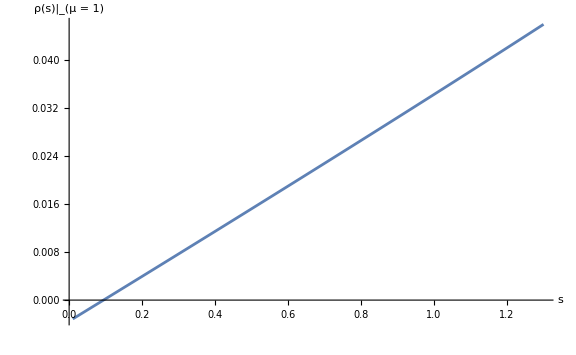
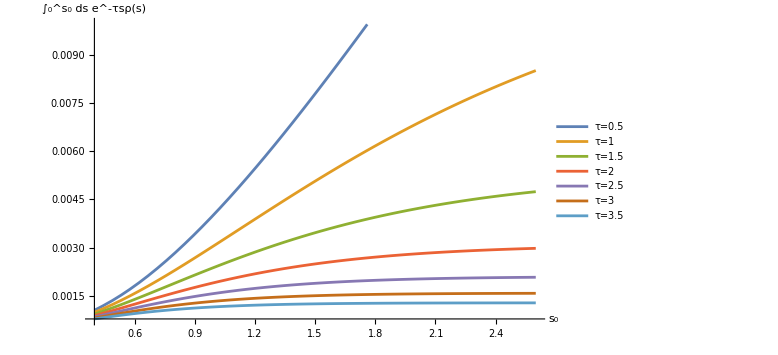

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

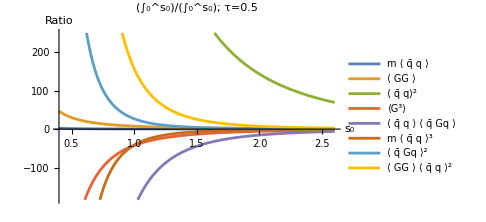
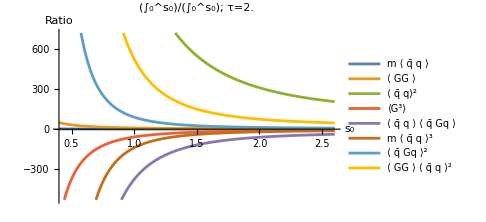
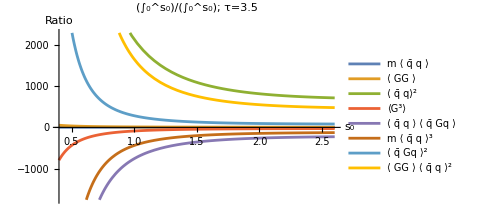

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

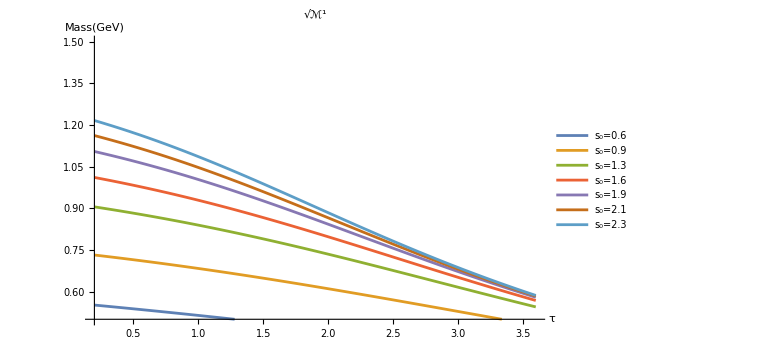
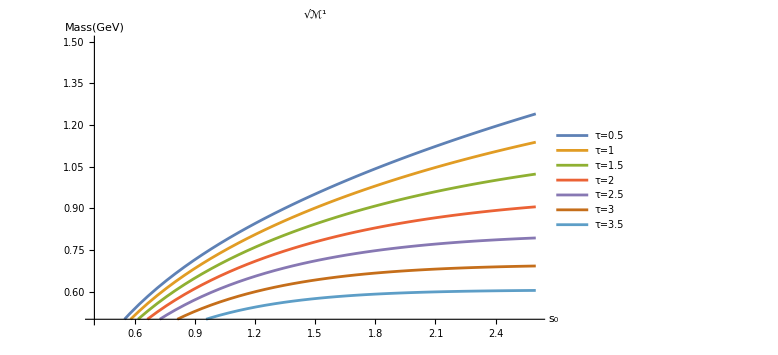

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

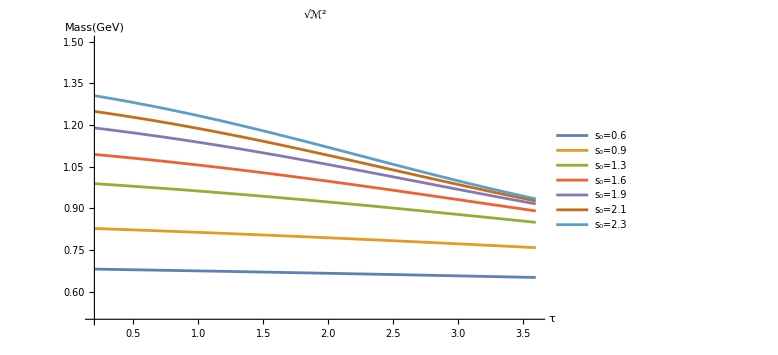
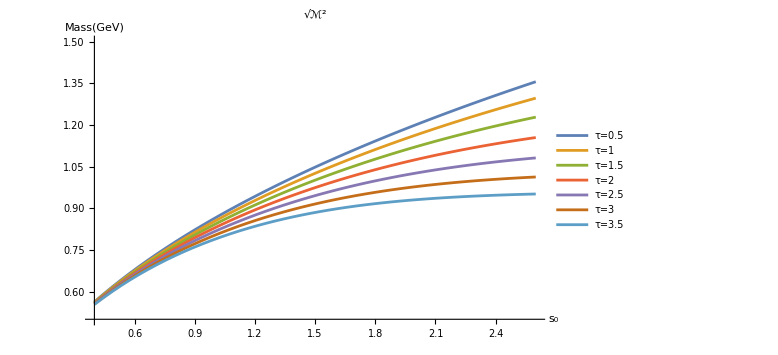

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

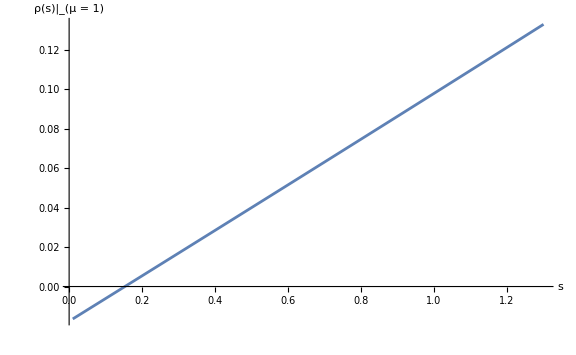
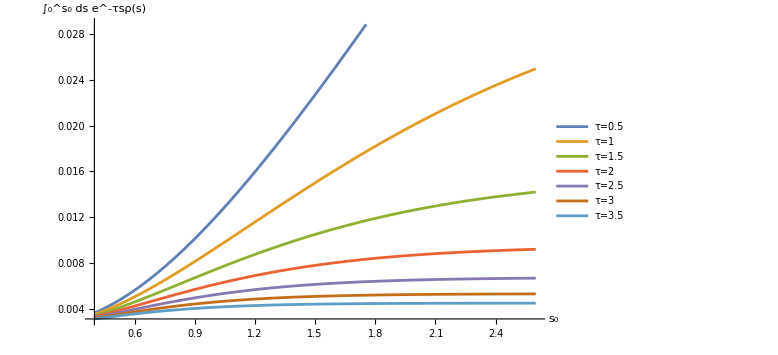

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

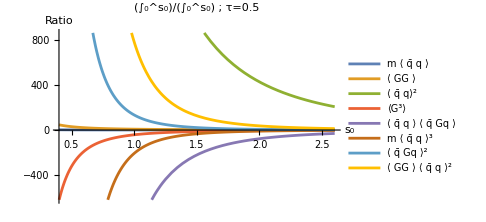
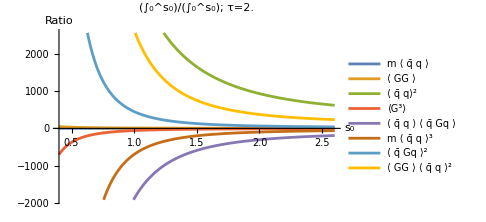
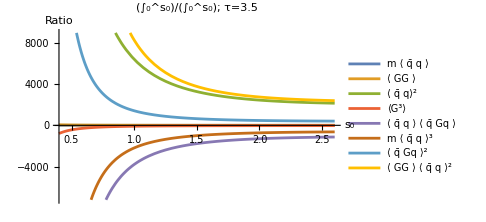

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

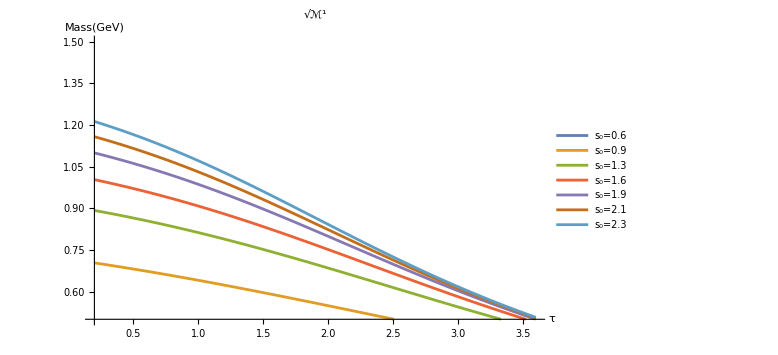
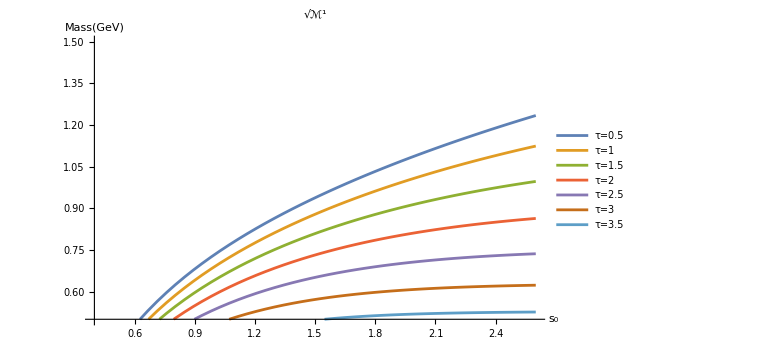

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5